```mathematica
a1 = {1,0,0};
a2 = {0,1,0};
a3 = {0,0,1};
```

```mathematica
L=11;
latt = Flatten[Table[n1*a1+n2*a2+n3*a3,{n1,L},{n2,1},{n3,L}],2];
mp=Mean[latt];
latt=Table[l-mp,{l,latt}];
```

```mathematica
Mean[latt]
```

{0,0,0}

```mathematica
df[r_]:=2 √r
```

```mathematica
Graphics3D[{{White,Sphere[#+0.5df[Norm[#[[;;2]]]]*a3,0.3]}}&/@latt]
```

-Graphics3D-

```mathematica
emw[d_,r_,ϕ_]:=ⅇ^(ⅈ*(d.r-ϕ))(* r in units of λ/2π*)
p1 = {1,0,0}; p2={0,1,0};
p1*emw[a1,r1*a1+r2*a2+r3*a3,0]+p1*emw[-a1,r1*a1+r2*a2+r3*a3,0]+p2*emw[a2,r1*a1+r2*a2+r3*a3,ϕ]+p2*emw[-a2,r1*a1+r2*a2+r3*a3,ϕ]
int=Refine[%. %*//ComplexExpand,r1∈Reals&&r2∈Reals&&r3∈Reals&&ϕ1∈Reals&&ϕ2∈Reals]//FullSimplify
rs=Table[i,{i,0,6π,2π/40}];
prof=Flatten[Table[{r1,r2,int/.{ϕ->0}//N},{r1,rs},{r2,rs}],1];
```

{ⅇ^(-ⅈ r1)+ⅇ^(ⅈ r1),ⅇ^(ⅈ (-r2-ϕ))+ⅇ^(ⅈ (r2-ϕ)),0}

2 (2+Cos[2 r1]+Cos[2 r2])

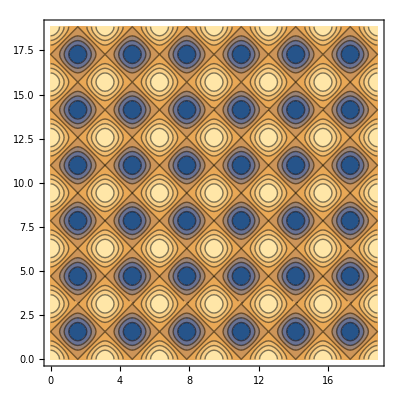

```mathematica
ListContourPlot[prof]
```

```mathematica
HTB[qu,qv,qz]=2tso*(Sin[qu]*σ[1]+Sin[qv]*σ[2])+(mz-2tz*Cos[qz]-t1(Cos[qu]+Cos[qv]))*σ[3]
```

2 tso (Sin[qu] σ[1]+Sin[qv] σ[2])+(mz-t1 (Cos[qu]+Cos[qv])-2 tz Cos[qz]) σ[3]

```mathematica
Series[HTB[qu,qv,qz],{qu,0,2},{qv,0,2},{qz,π/2,2}]//Normal
```

2 qu tso σ[1]+2 qv tso σ[2]+(mz-2 t1) σ[3]+1/2 qu^2 t1 σ[3]+1/2 qv^2 t1 σ[3]+2 (-π/2+qz) tz σ[3]

```mathematica
Series[HTB[qu,qv,qz]/.{mz->1,t1->1,tz->1},{qu,0,1},{qv,0,1},{qz,π/2,1}]//Normal
```

2 qu tso σ[1]+2 qv tso σ[2]-σ[3]+2 (-π/2+qz) σ[3]